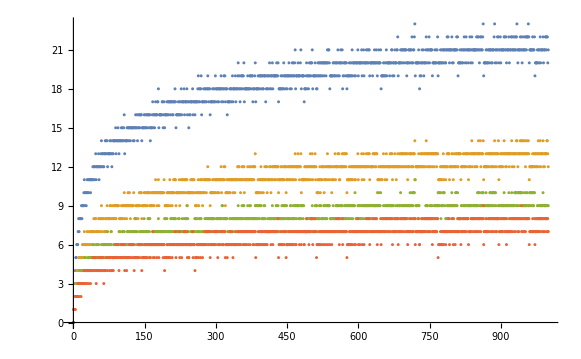

```mathematica
Sums[n_]:=Table[{i,n-i},{i,n/2}]
Prods[n_]:=DeleteCases[Table[If[Divisible[n,i],{i,n/i}],{i,2,Sqrt[n]}],Null]

Costs[costs_,n_]:=Module[{i,res=costs},
For[i=2,i<=n,i++,
m=Min[Map[res[#[[1]]]+res[#[[2]]]&,Join[Sums[i],Prods[i]]]];
If[m<res[i]||MissingQ[res[i]],AssociateTo[res,i->m]]
];
Return[res]
]

ListPlot[{KeyValueMap[{#1,#2}&,Costs[<|0->0,1->1|>,1000]],KeyValueMap[{#1,#2}&,Costs[<|0->0,1->1,2->1|>,1000]],KeyValueMap[{#1,#2}&,Costs[<|0->0,1->1,2->1,3->1|>,1000]],KeyValueMap[{#1,#2}&,Costs[<|0->0,1->1,2->1,3->1,4->1|>,1000]]}]
```

```mathematica
Pairs[g_,cayleyTable_List]:=DeleteCases[Flatten[Table[If[cayleyTable[[i,j]]==g,{cayleyTable[[1,i]],cayleyTable[[1,j]]}],{i,Length[cayleyTable]},{j,Length[cayleyTable]}],1],Null]
Invert[g_,cayleyTable_List]:=DeleteCases[Table[If[cayleyTable[[Flatten[Position[cayleyTable[[1]],g]][[1]],i]]==cayleyTable[[1,1]],cayleyTable[[1,i]]],{i,Length[cayleyTable]}],Null][[1]]

(*INPUT: association of generators with costs & multiplication table
OUTPUT: association of all elements of finite monoid with costs*)
GenFinMonoid[cost_Association,multTable_]:=Module[{elements=multTable[[1]],len=Length[multTable],i,currCost=cost,prevCost},
Until[prevCost==currCost,
prevCost=currCost;
For[i=1,i<=len,i++,
AssociateTo[currCost,elements[[i]]->Min[Select[Map[currCost[#[[1]]]+currCost[#[[2]]]&,Pairs[elements[[i]],multTable]],FreeQ[#,_Missing|_Plus]&]]]
]
];
Return[currCost]
]

(*INPUT: association of generators with costs & Cayley table
OUTPUT: association of all elements of finite group with costs*)
GenFinGroup[cost_Association,cayleyTable_]:=Module[{elements=cayleyTable[[1]],len=Length[cayleyTable],i,currCost=cost,prevCost},
Until[prevCost==currCost,
prevCost=currCost;
For[i=1,i<=len,i++,
AssociateTo[currCost,elements[[i]]->Min[Select[Append[Map[currCost[#[[1]]]+currCost[#[[2]]]&,Pairs[elements[[i]],cayleyTable]],currCost[Invert[elements[[i]],cayleyTable]]+1],FreeQ[#,_Missing|_Plus]&]]]
]
];
Return[currCost]
]

(*INPUT: association of generators with costs, addition table, & multiplication table excluding the rows and columns with all 0's, since 0 is an annihilator
OUTPUT: association of all elements of finite rig with costs*)
GenFinRig[cost_Association,sumTable_,prodTable_]:=Module[{elements=sumTable[[1]],len=Length[sumTable],i,currCost=cost,prevCost},
Until[prevCost==currCost,
prevCost=currCost;
For[i=1,i<=len,i++,
AssociateTo[currCost,elements[[i]]->Min[Select[Map[currCost[#[[1]]]+currCost[#[[2]]]&,Join[Pairs[elements[[i]],sumTable],Pairs[elements[[i]],prodTable]]],FreeQ[#,_Missing|_Plus]&]]]
]
];
Return[currCost]
]

(*INPUT: association of generators with costs, addition table, & multiplication table excluding the rows and columns with all 0's, since 0 is an annihilator
OUTPUT: association of all elements of finite ring with costs*)
GenFinRing[cost_Association,sumTable_,prodTable_]:=Module[{elements=sumTable[[1]],len=Length[sumTable],i,currCost=cost,prevCost},
Until[prevCost==currCost,
prevCost=currCost;
For[i=1,i<=len,i++,
AssociateTo[currCost,elements[[i]]->Min[Select[Append[Map[currCost[#[[1]]]+currCost[#[[2]]]&,Join[Pairs[elements[[i]],sumTable],Pairs[elements[[i]],prodTable]]],currCost[Invert[elements[[i]],sumTable]]+1],FreeQ[#,_Missing|_Plus]&]]]
]
];
Return[currCost]
]

(*INPUT: association of generators with costs, addition table, & multiplication table excluding the rows and columns with all 0's, since 0 is an annihilator
OUTPUT: association of all elements of finite field with costs*)
GenFinSkewField[cost_Association,sumTable_,prodTable_]:=Module[{elements=sumTable[[1]],len=Length[sumTable],i,currCost=cost,prevCost},
Until[prevCost==currCost,
prevCost=currCost;
For[i=1,i<=len,i++,
AssociateTo[currCost,elements[[i]]->Min[Select[Append[Append[Map[currCost[#[[1]]]+currCost[#[[2]]]&,Join[Pairs[elements[[i]],sumTable],Pairs[elements[[i]],prodTable]]],currCost[Invert[elements[[i]],sumTable]]+1],currCost[Invert[elements[[i]],prodTable]]+1],FreeQ[#,_Missing|_Plus]&]]]
]
];
Return[currCost]
]
```

562.484

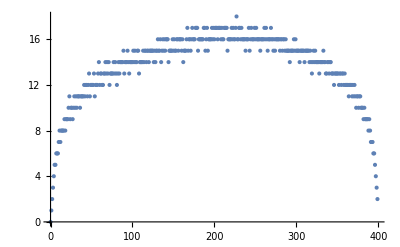

```mathematica
n=400;
mySumTable=Table[Table[Mod[i+j,n],{i,0,n-1}],{j,0,n-1}];
myProdTable=Table[Table[Mod[i*j,n],{i,1,n-1}],{j,1,n-1}];
Cost=<|0->0,1->1|>;

Cost=Timing[GenFinRing[Cost,mySumTable,myProdTable]];
Cost[[1]]
Cost=Cost[[2]];

ListPlot[KeyValueMap[{#1,#2}&,Cost]]
Grid[KeyValueMap[{#1,#2}&,Cost]];
```

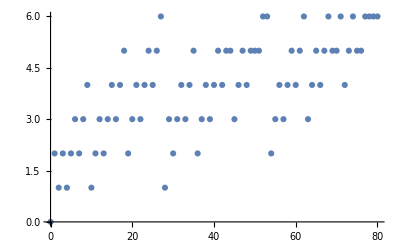

(0 | 0
0 | 0) | 0 | 0
(1 | 0
0 | 0) | 1 | 0
(0 | 1
0 | 0) | 1 | 0
(0 | 0
1 | 0) | 1 | 0
(0 | 0
0 | 1) | 1 | 0
(1 | 0
0 | 1) | 2 | 0
(0 | 0
0 | 2) | 2 | 0
(0 | 0
1 | 1) | 2 | 0
(0 | 0
1 | 2) | 3 | 0
(0 | 0
2 | 0) | 2 | 0
(0 | 0
2 | 1) | 3 | 0
(0 | 0
2 | 2) | 4 | 0
(0 | 1
0 | 1) | 2 | 0
(0 | 1
0 | 2) | 3 | 0
(0 | 1
1 | 0) | 2 | 0
(0 | 1
1 | 1) | 3 | 0
(0 | 1
1 | 2) | 4 | 0
(0 | 1
2 | 0) | 3 | 0
(0 | 1
2 | 1) | 4 | 0
(0 | 1
2 | 2) | 5 | 0
(0 | 2
0 | 0) | 2 | 0
(0 | 2
0 | 1) | 3 | 0
(0 | 2
0 | 2) | 4 | 0
(0 | 2
1 | 0) | 3 | 0
(0 | 2
1 | 1) | 4 | 0
(0 | 2
1 | 2) | 5 | 0
(0 | 2
2 | 0) | 4 | 0
(0 | 2
2 | 1) | 5 | 0
(0 | 2
2 | 2) | 6 | 0
(1 | 0
0 | 2) | 3 | 0
(1 | 0
1 | 0) | 2 | 0
(1 | 0
1 | 1) | 3 | 0
(1 | 0
1 | 2) | 4 | 0
(1 | 0
2 | 0) | 3 | 0
(1 | 0
2 | 1) | 4 | 0
(1 | 0
2 | 2) | 5 | 0
(1 | 1
0 | 0) | 2 | 0
(1 | 1
0 | 1) | 3 | 0
(1 | 1
0 | 2) | 4 | 0
(1 | 1
1 | 0) | 3 | 0
(1 | 1
1 | 1) | 4 | 0
(1 | 1
1 | 2) | 5 | 0
(1 | 1
2 | 0) | 4 | 0
(1 | 1
2 | 1) | 5 | 0
(1 | 1
2 | 2) | 5 | 1
(1 | 2
0 | 0) | 3 | 0
(1 | 2
0 | 1) | 4 | 0
(1 | 2
0 | 2) | 5 | 0
(1 | 2
1 | 0) | 4 | 0
(1 | 2
1 | 1) | 5 | 0
(1 | 2
1 | 2) | 5 | 1
(1 | 2
2 | 0) | 5 | 0
(1 | 2
2 | 1) | 6 | 0
(1 | 2
2 | 2) | 6 | 1
(2 | 0
0 | 0) | 2 | 0
(2 | 0
0 | 1) | 3 | 0
(2 | 0
0 | 2) | 4 | 0
(2 | 0
1 | 0) | 3 | 0
(2 | 0
1 | 1) | 4 | 0
(2 | 0
1 | 2) | 5 | 0
(2 | 0
2 | 0) | 4 | 0
(2 | 0
2 | 1) | 5 | 0
(2 | 0
2 | 2) | 6 | 0
(2 | 1
0 | 0) | 3 | 0
(2 | 1
0 | 1) | 4 | 0
(2 | 1
0 | 2) | 5 | 0
(2 | 1
1 | 0) | 4 | 0
(2 | 1
1 | 1) | 5 | 0
(2 | 1
1 | 2) | 6 | 0
(2 | 1
2 | 0) | 5 | 0
(2 | 1
2 | 1) | 5 | 1
(2 | 1
2 | 2) | 6 | 1
(2 | 2
0 | 0) | 4 | 0
(2 | 2
0 | 1) | 5 | 0
(2 | 2
0 | 2) | 6 | 0
(2 | 2
1 | 0) | 5 | 0
(2 | 2
1 | 1) | 5 | 1
(2 | 2
1 | 2) | 6 | 1
(2 | 2
2 | 0) | 6 | 0
(2 | 2
2 | 1) | 6 | 1
(2 | 2
2 | 2) | 6 | 2

```mathematica
n=3;
myElements=Insert[DeleteElements[Tuples[Tuples[{Range[n]-1,Range[n]-1}],2],{IdentityMatrix[2]}],IdentityMatrix[2],2];
mySumTable=Table[Table[Mod[i+j,n],{i,myElements}],{j,myElements}];
myProdTable=Table[Table[Mod[i.j,n],{i,Delete[myElements,1]}],{j,Delete[myElements,1]}];
Cost=<|{{0,0},{0,0}}->0,{{1,0},{0,0}}->1,{{0,1},{0,0}}->1,{{0,0},{1,0}}->1,{{0,0},{0,1}}->1|>;

Grid[mySumTable];
Grid[myProdTable];

Cost=GenFinRig[Cost,mySumTable,myProdTable];
ListPlot[KeyValueMap[{Flatten[Position[mySumTable[[1]],#1]][[1]]-1,#2}&,Cost]]
Grid[KeyValueMap[{MatrixForm[#1],#2}&,Cost]]
```